#### Find the closest path between two elastic maps INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook Variables to change: Tmat, dt, ListSigma

#### choose Tmat

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatDefeat;
```

```mathematica
Tmat=TmatRussell;
```

```mathematica
Tmat=TmatBrownTypo;
```

```mathematica
Tmat=TmatBrown;
```

#### check that it’s symmetric, display info

```mathematica
MatrixNote[Tmat]
Tmat==Transpose[Tmat]
PrintVoigt[Tmat]
```

#### Set of Sigmas to use For the plotting, it’d be helpful to list these in order from TRIV (smallest beta) to ISO (largest beta).

```mathematica
ListSigma={ORTH,TET};
```

```mathematica
ListSigma={MONO,ORTH}; (* Brown parabolas on XISO path *)
```

```mathematica
ListSigma={TET}; (* Brown parabola on CUBE path *)
```

```mathematica
ListSigma={MONO};
```

```mathematica
ListSigma={TET,TRIG,MONO}; (* Brown TRIG triangle on TRIG path *)
```

```mathematica
ListSigma={ISO,CUBE,XISO,TRIG,TET,ORTH,MONO,TRIV};
```

```mathematica
ListSigma={TRIV,MONO,TRIG,ORTH,TET,CUBE,XISO,ISO};
```

#### Closest T to ISO

```mathematica
WantDetails="WantDetails";
```

```mathematica
MatrixNote[Tmat]
betaISO =βTinitial[Tmat,ISO]/Degree  (* AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree *)
TISO =Closest[Tmat,ISO];  (* ProjToVSigOfU[Tmat,id,ISO]*)
MatrixForm[TISO]
```

#### Choose Tmat1 (low symmetry) and Tmat2 (high symmetry)

```mathematica
MatrixNote[Tmat]
Tmat1 =Tmat ;
Tmat2 =TISO;
```

#### defaults for custom plotting

```mathematica
Sig1=TRIV;Sig2=ISO;
ttop = 0.5;
```

#### Example: Brown TET triangle (supp1) TET to XISO segment for the Brown map Here TXISO is the closest to TRIV (Pathway 2), and β_XISO = 20.35^o

```mathematica
MatrixNote[Tmat]
Sig1=TET;
Sig2=XISO;
OutputFor[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
OutputFor[Tmat,Sig2]
TXISO=Closest[Tmat,Sig2];
Tmat1=TTET;
Tmat2=TXISO; 
ListSigma={TET,XISO}; 
ttop = 0.611707;
```

#### Example: Brown TET parabola (supp2) TET to CUBE segment for the Brown map Here TCUBE is the closest to TRIV (Pathway 2), and β_CUBE = 24.34^o

```mathematica
(* MatrixNote[Tmat]
Sig1=TET;
Sig2=CUBE; 
OutputFor[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
OutputFor[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTET ;
Tmat2=TCUBE;
ListSigma={TET}; *)
```

#### Example: Brown TRIG triangle (supp3) TRIG to CUBE segment for the Brown map Here CUBE is the closest to TRIV (Pathway 2), and β_CUBE = 21.12^o

```mathematica
(* MatrixNote[Tmat]
Sig1=TRIG;
Sig2=CUBE; 
OutputFor[Tmat,Sig1]
TTRIG=Closest[Tmat,Sig1];
OutputFor[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTRIG;
Tmat2=TCUBE;
ListSigma={TET,TRIG,MONO};
ttop=0.53515; *)
```

#### KEY FUNCTION

```mathematica
TT[t_,Tmat1_,Tmat2_]:=(1-t) Tmat1+t Tmat2
```

#### check endpoints (but not that your chosen t values may exclude the endpoints)

```mathematica
MatrixNote[Tmat]
MatrixForm[Tmat1]
MatrixForm[TT[0,Tmat1,Tmat2]]
MatrixForm[Tmat2]
MatrixForm[TT[1,Tmat1,Tmat2]]
```

#### t values to use (note: you can choose to use t2 > 1 for the custom set of available maps)

```mathematica
t1 = 1; t2=1.1;dt =0.01;   (* Igel -- show that t > 1 *)
t1 = 0; t2=1;
dt =0.5;
dt = 0.02;
Ranget=Range[t1,t2,dt];
```

```mathematica
t1 = 0.42; t2 = 0.44;dt=0.005;  (* Brown TET triangle - Pathway 2 *)
(* t1 = 0.38; t2 = 0.40;dt = 0.005; *)  (* Brown TET triangle - Pathway 3 *)
t1 = 0.41; t2 = 0.45;dt=0.005; 
Ranget=Range[t1,t2,dt];
(* Ranget=Join[{0},Range[t1,t2,dt],{1}] *)
```

```mathematica
t1 = 11; t2 = 1+tpert[Tmat];dt=0.05; 
Ranget=Range[t1,t2,dt];
```

```mathematica
t1 = 0.; t2 = 1.;dt=0.05; 
(* t1 = -tpert[Tmat]; *)
Ranget=Range[t1,t2,dt];
```

#### min and max values of t (these are used for plotting)

```mathematica
Ranget
tmin=Ranget[[1]]
tmax=Ranget[[Length[Ranget]]]
```

#### Display the set of Tmats as BB and as Voigt

```mathematica
MatrixNote[Tmat]
(Print["t = ",# ]; PrintVoigt[TT[#,Tmat1,Tmat2]])&/@Ranget
```

## Optional: Choose an orientation for all the balls based on the closest XISO (or whatever you want).

#### commands copied from LatticeOfClosestMaps.nb Display the set of REORIENTED Tmats as BB and as Voigt

```mathematica
(* WantDetails="WantDetails";
OutputFor[Tmat,XISO]
MatrixForm[UT[Tmat,XISO]]
MatrixForm[Closest[Tmat,XISO]]
OutputFor[Closest[Tmat,XISO],XISO]
Ux=IdentityMatrix[3];
(* Ux=UT[Closest[Tmat,XISO],XISO]; *)
MatrixForm[Ux]
Ubarx=MatrixUbar[Ux];
MatrixForm[Chop[Ubarx,.0001]]
(Print["t = ",# ]; PrintVoigt[Transpose[Ubarx].TT[#,Tmat1,Tmat2].Ubarx])&/@Ranget *)
```

## Proceed with Tmat in its original orientation

```mathematica
Ux=IdentityMatrix[3];
Ubarx=MatrixUbar[Ux];
```

## Example functions (none of these are needed)

#### Example of plotting two sets of points on one plot.

```mathematica
fff[t_,Sigma_]:=t/2
```

```mathematica
Graphics[{PointSize[.02],
Table[Point[{t,0}],                    {t,.2,.8,.2}],
Table[Point[{t,fff[t,XISO]}],{t,.2,.8,.2}],
Table[Point[{t,fff[t,ORTH]}],{t,.2,.8,.2}]},Axes->True,AxesOrigin->{0,0}]
```

#### Examples: Closest to MONO for some chosen t (not necessarily the t in Ranget)

```mathematica
tpicks ={0,1,tmax};
tpicks={0.2};
Sigma=MONO;
(* OutputFor[TT[#,Tmat1,Tmat2],Sigma]&/@tpicks *)
Do[(Print["t = ",tpicks[[i]]];OutputFor[TT[tpicks[[i]],Tmat1,Tmat2],Sigma]),{i,1,Length[tpicks]}]
```

#### Test Tmat (from above)

```mathematica
Ttest=TT[tpicks[[Length[tpicks]]],Tmat1,Tmat2];
MatrixForm[Ttest]
```

#### This is the rotation from the minimization.

```mathematica
(* UT[Tmat,Σ] *)
```

#### This is the corresponding elastic map.

```mathematica
(* MatrixForm[ProjToVSigOfU[Tmat,UT[Tmat,Σ],Σ]] *)
```

#### This command is in the common_funs file.

```mathematica
(* Closest[Tmat_,Sigma_]:=ProjToVSigOfU[Tmat,UT[Tmat,Sigma],Sigma]; *)
```

#### This is the angle between Tmat and the closest Sigma map.

```mathematica
(* AngleMatrix[Tmat,Closest[Tmat,Sigma]] *)
```

#### This is the first matrix in OutputFor

```mathematica
MatrixForm[UT[Ttest,MONO]]
```

#### This is the last matrix in OutputFor (Closest[Tmat,Sigma] is defined in common_funs.nb)

```mathematica
MatrixForm[Closest[Ttest,MONO]]
```

#### These are the βs in OutputFor

```mathematica
AngleMatrix[Ttest,Closest[Ttest,MONO]]/Degree
βT[Ttest,MONO]/Degree
```

## Calculate distance to each symmetry class KEY COMMAND: OutputFor performs the key calculations (minimizations)

```mathematica
WantDetails="NoWantDetails";
```

```mathematica
Ranget
```

```mathematica
ListSigma
```

```mathematica
(* OutputFor[TT[Ranget[[1]],Tmat1,Tmat2],ListSigma[[1]]] *) (* example of one OutputFor *)
```

```mathematica
Do[(Print["t = ",Ranget[[i]]];OutputFor[TT[Ranget[[i]],Tmat1,Tmat2],#])&/@ListSigma,{i,1,Length[Ranget]}]
```

## Optional: Plot the balls (this was motivated by the Brown TET triangle)

```mathematica
eye=10xyzTP[{30Degree,75Degree}];
plotpoints=10;
```

#### overwrite the default coloring for this Tmat (see chooseTmat.nb) cpMONO is in common_funs.nb; it requires defining the contours

```mathematica
Clear[contours,MaxForScaling]
```

```mathematica
contours[Tmat]=Range[0,20,2]
MaxForScaling[Tmat]=20
```

```mathematica
(* Show[cpMONO[TT[Ranget[[1]],Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye] *)
```

#### function for plotting the U matrix (columns) For Sigma ≠ TRIV, Udots[Tmat, Sigma] should give the high symmetry axis (green) of a closest Sigma map to Tmat. For Sigma ≠ TRIV, MONO, Udots[Tmat, Sigma] should also give 2-fold axes (red, blue) of a closest Sigma map to Tmat.

```mathematica
Udots[Tmat_,Sigma_]:=Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.03],{ 
{Red,     Point[UT[Tmat, Sigma].{1,0,0}],Point[UT[Tmat, Sigma].{-1,0,0}]},
{Blue,   Point[UT[Tmat, Sigma].{0,1,0}],Point[UT[Tmat, Sigma].{0,-1,0}]},
{Green,Point[UT[Tmat, Sigma].{0,0,1}],Point[UT[Tmat, Sigma].{0,0,-1}]}}},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

#### main plot (Sig1 and Sig2 should be specified at the top)

```mathematica
If[Length[Ranget] <12,
{Show[cpMONO[TT[#,Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye]&/@Ranget;
Udots[TT[#,Tmat1,Tmat2],Sig1]&/@Ranget;
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],Sig1],  contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye]&/@Ranget; 
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],Sig2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye]&/@Ranget}]
```

#### plot the U dots on a pair of plots for points on either side of the triangle (ttop should be specified at the top)

```mathematica
Ranget
```

```mathematica
Ranget1=Select[Ranget,#<=ttop&]    (* Note ≤ *)
Ranget2=Select[Ranget,#>ttop&]
```

```mathematica
ListMat1=TT[#,Tmat1,Tmat2]&/@Ranget1;
ListMat2=TT[#,Tmat1,Tmat2]&/@Ranget2;
```

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
MatrixForm[UT[#,Sig1]]&/@ListMat1
Print["Ranget2 = ",Ranget2];
MatrixForm[UT[#,Sig1]]&/@ListMat2
```

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,Sig1].{1,0,0}],Point[UT[#,Sig1].{-1,0,0}]},
{Blue,   Point[UT[#,Sig1].{0,1,0}],Point[UT[#,Sig1].{0,-1,0}]},
{Green,Point[UT[#,Sig1].{0,0,1}],Point[UT[#,Sig1].{0,0,-1}]}}&/@ListMat1},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
Print["Ranget2 = ",Ranget2];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,Sig1].{1,0,0}],Point[UT[#,Sig1].{-1,0,0}]},
{Blue,   Point[UT[#,Sig1].{0,1,0}],Point[UT[#,Sig1].{0,-1,0}]},
{Green,Point[UT[#,Sig1].{0,0,1}],Point[UT[#,Sig1].{0,0,-1}]}}&/@ListMat2},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

## Beta curves

```mathematica
ipick =1;
ListSigma
Sigpick=ListSigma[[ipick]]
MatrixNote[Tmat]
Ranget
```

```mathematica
ColumnForm[{PaddedForm[#,{2,2}],Round[βT[TT[#,Tmat1,Tmat2],Sigpick]/Degree,.001]}&/@Ranget]
```

#### Angle in radians between Tmat and the closest-Sigma to Tmat is βT[Tmat, Sigma]

```mathematica
MatrixNote[Tmat]
βT[Tmat,Sigpick]
%/Degree
```

#### Plot all the beta curves together.

```mathematica
line[Sigma_]:=Line[{#,βT[TT[#,Tmat1,Tmat2],Sigma]/Degree}&/@Ranget];
```

#### This simple plot should always work (With the Closest maps pre-saved, the plotting should be quick.)

```mathematica
(* Ranget *)
```

```mathematica
(* line/@ListSigma *)
```

```mathematica
MatrixNote[Tmat]
ListSigma
Graphics[line/@ListSigma,Axes->True,AspectRatio->1,ImageSize->200]
```

#### Or pick only one from ListSigma (see ipick above)

```mathematica
line[Sigpick]
Graphics[line[Sigpick],Axes->True,AspectRatio->.8,ImageSize->200]
```

```mathematica
xran =Ranget[[Length[Ranget]]]-Ranget[[1]]
```

```mathematica
Max[Ranget]
```

```mathematica
Ranget
```

#### The fancier version has colored dots (hues are set in chooseTmat.nb)

```mathematica
PtOnβcurve[t_,Σ_]:={t,βT[TT[t,Tmat1,Tmat2],Σ]/Degree};
BetaCurve[Ranget_,Σ_]:={Point/@Table[PtOnβcurve[Ranget[[n]],Σ],{n,1,Length[Ranget]}]};     
yvals=βT[TT[#,Tmat1,Tmat2],ListSigma[[1]]]/Degree &/@ Ranget; (* based on the first Σ in the list *)
ymin=Min[yvals];
ymax=Max[yvals];
xmin=Min[Ranget];
xmax=Max[Ranget];
xran =xmax-xmin;
btextx=xmin-0.05xran; (* btextx=1.03tmax; *)
ylabelx=xmin-0.35xran; 
ylabely =0.5(ymin+ymax);
xlabelx=(Max[Ranget]+Min[Ranget])/2;
xlabely =-0.1ymax;
```

```mathematica
ListSigma
```

```mathematica
xlabely
```

```mathematica
Graphics[{PointSize[.02],
line/@ListSigma,
{hue[#],BetaCurve[Ranget,#]}&/@ListSigma,
Text[Style[SequenceForm[BetaText[#]," (",Round[βT[TT[tmin,Tmat1,Tmat2],#]/Degree,0.01],")"],{hue[#],15}], (* the text *)
                                                {btextx,βT[TT[tmin,Tmat1,Tmat2],#]/Degree},{1,0}]&/@ListSigma,  (* the location of the text *)
Text[Style["β_Σ(t), degrees",22],{ylabelx,ylabely},{0,0},{0,1}], (* y-axis label *)
Text[Style["t",22],{xlabelx,xlabely},{0,0}] (* y-axis label *)
},
Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->600]
```

#### Pick one (your pick has to be from ListSigma)

```mathematica
Sig={TET};
```

```mathematica
Graphics[{PointSize[.02],
line/@Sig,
{hue[#],BetaCurve[Ranget,#]}&/@Sig,
Text[Style[SequenceForm[BetaText[#]," (",Round[βT[TT[tmin,Tmat1,Tmat2],#]/Degree,0.01],")"],{hue[#],12}],
                                                {btextx,βT[TT[tmin,Tmat1,Tmat2],#]/Degree},{1,0}]&/@Sig},
Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->300]
```

## For reference

#### BrownNew: t=0 to t=1, dt = 0.05, ListSigma = all

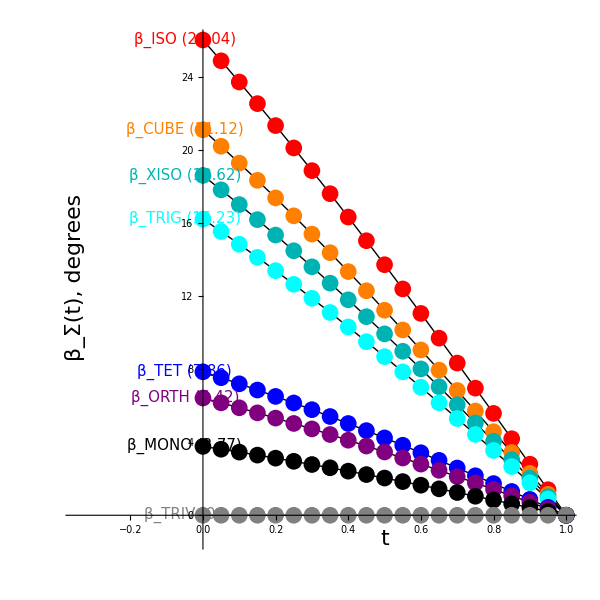

#### BrownNew: dt = 0.05, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET,XISO}

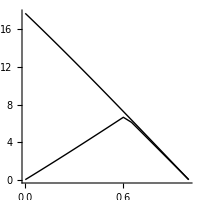

#### BrownNew: dt = 0.05, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET,XISO}

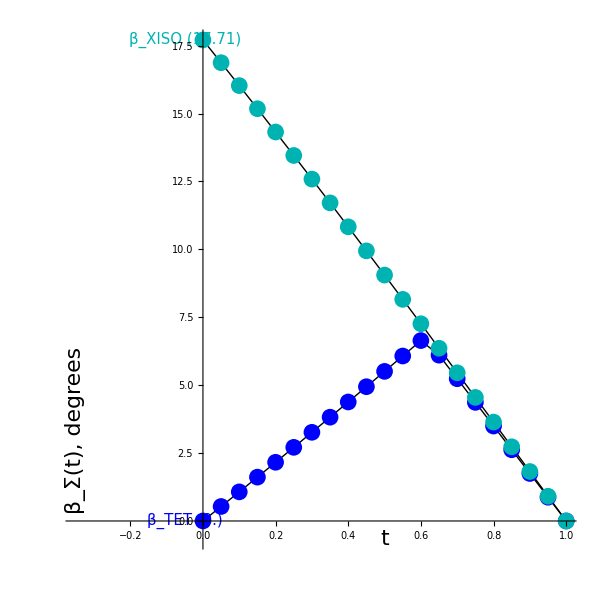

#### BrownTypo: dt = 0.05, Tmat1=TCUBE, Tmat2=TTET, ListSigma = {TET} NEEDS UPDATING

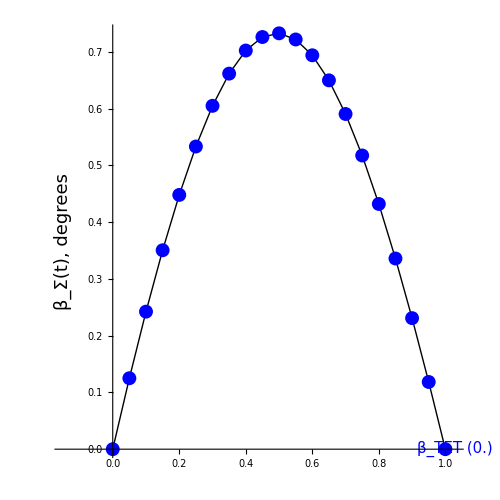

#### BrownNew: dt = 0.05, Tmat1=TCUBE, Tmat2=TTRIG, ListSigma = {TRIG,TET} NEEDS UPDATING